Exercises for Section 12 | Sound

Generate the sequence of notes with pitches 0, 4 and 7. |

EXPECTED OUTPUT »

-Graphics- | ×

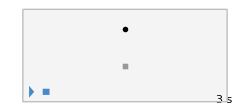

```mathematica
Sound[{SoundNote[0],SoundNote[4],SoundNote[7]}]
```

Generate 2 seconds of playing middle A on a cello. |

EXPECTED OUTPUT »

-Graphics- | ×

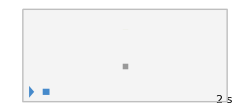

```mathematica
Sound[SoundNote["A",2,"Cello"]]
```

Generate a “riff” of notes from pitch 0 to pitch 48 in steps of 1, with each note lasting 0.05 seconds. |

EXPECTED OUTPUT »

-Graphics- | ×

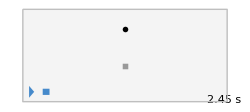

```mathematica
Sound[Table[SoundNote[n,0.05],{n,0,48,1}]]
```

Generate a sequence of notes going from pitch 12 down to 0 in steps of 1. |

EXPECTED OUTPUT »

-Graphics- | ×

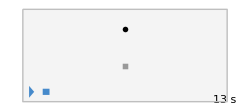

```mathematica
Sound[Table[SoundNote[pitch],{pitch,12,0,-1}]]
```

Generate a sequence of 5 notes starting with middle C, then successively going up by an octave at a time. |

EXPECTED OUTPUT »

-Graphics- | ×

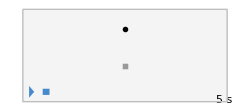

```mathematica
Sound[Table[SoundNote[n],{n,{0,12,24,36,42}}]];
Sound[Table[SoundNote[n],{n,0,54,12}]]
```

Generate a sequence of 10 notes on a trumpet with random pitches from 0 to 12 and duration 0.2 seconds. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

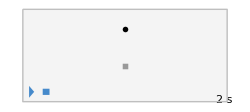

```mathematica
Sound[Table[SoundNote[RandomInteger[{0,12}],0.2,"Trumpet"],10]]
```

Generate a sequence of 10 notes with random pitches up to 12 and random durations up to 10 tenths of a second. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

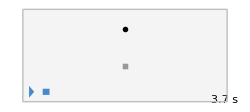

```mathematica
Sound[Table[SoundNote[RandomInteger[{0,12}],RandomInteger[{0,10}]/10],10]]
```

Generate 0.1-second notes with pitches given by the digits of 2^31. |

EXPECTED OUTPUT »

-Graphics- | ×

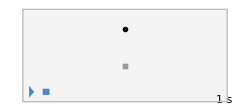

```mathematica
Sound[Table[SoundNote[n,0.1],{n,{2,1,4,7,4,8,3,6,4,8}}]]
```

Create a sound from the letters in CABBAGE, each playing for 0.3 seconds sounding like a guitar. |

EXPECTED OUTPUT »

-Graphics- | ×

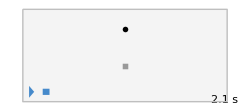

```mathematica
Sound[Table[SoundNote[n,0.3,"Guitar"],{n,Characters["CABBAGE"]}]]
```

Generate 0.1-second notes with pitches given by the letter numbers of the characters in “wolfram”. |

EXPECTED OUTPUT »

-Graphics- | ×

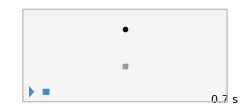

```mathematica
Sound[Table[SoundNote[p,0.1],{p,LetterNumber["wolfram"]}]]
```

Generate a sequence of three notes of 1 second of playing middle D on the cello, piano and guitar.  |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Sound[{SoundNote["D",1,"Cello"],SoundNote["D",1,"Piano"],SoundNote["D",1,"Guitar"]}]
```

-Graphics-

Generate a sequence of notes from pitch 0 to pitch 12, going up in steps of 3.  |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Sound[Table[SoundNote[p],{p,0,12,3}]]
```

-Graphics-

Generate a sequence of 5 notes starting with middle C, then successively going up by a perfect fifth (7 semitones) at a time.  |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Sound[Table[SoundNote[p],{p,0,28,7}]]
```

-Graphics-

Generate 0.02-second notes with pitches given by the lengths of the names of integers from 1 to 200. |

EXPECTED OUTPUT »

-Graphics- | ×

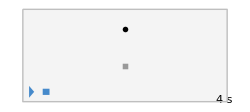

```mathematica
Sound[Table[SoundNote[p,0.02],{p,{3,3,5,4,4,3,5,5,4,3,6,6,8,8,7,7,9,8,8,6,10,10,12,11,11,10,12,12,11,6,10,10,12,11,11,10,12,12,11,5,9,9,11,10,10,9,11,11,10,5,9,9,11,10,10,9,11,11,10,5,9,9,11,10,10,9,11,11,10,7,11,11,13,12,12,11,13,13,12,6,10,10,12,11,11,10,12,12,11,6,10,10,12,11,11,10,12,12,11,11,15,15,17,16,16,15,17,17,16,15,18,18,20,20,19,19,21,20,20,18,22,22,24,23,23,22,24,24,23,18,22,22,24,23,23,22,24,24,23,17,21,21,23,22,22,21,23,23,22,17,21,21,23,22,22,21,23,23,22,17,21,21,23,22,22,21,23,23,22,19,23,23,25,24,24,23,25,25,24,18,22,22,24,23,23,22,24,24,23,18,22,22,24,23,23,22,24,24,23,11}}]]
```

```mathematica
Sound[Table[SoundNote[p,0.02],{p,{Table[p,{p,1,200}]}}]];
```

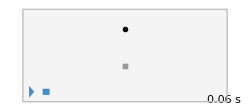

-Graphics-

{3,3,5,4,4,3,5,5,4,3,6,6,8,8,7,7,9,8,8,6,10,10,12,11,11,10,12,12,11,6,10,10,12,11,11,10,12,12,11,5,9,9,11,10,10,9,11,11,10,5,9,9,11,10,10,9,11,11,10,5,9,9,11,10,10,9,11,11,10,7,11,11,13,12,12,11,13,13,12,6,10,10,12,11,11,10,12,12,11,6,10,10,12,11,11,10,12,12,11,11,15,15,17,16,16,15,17,17,16,15,18,18,20,20,19,19,21,20,20,18,22,22,24,23,23,22,24,24,23,18,22,22,24,23,23,22,24,24,23,17,21,21,23,22,22,21,23,23,22,17,21,21,23,22,22,21,23,23,22,17,21,21,23,22,22,21,23,23,22,19,23,23,25,24,24,23,25,25,24,18,22,22,24,23,23,22,24,24,23,18,22,22,24,23,23,22,24,24,23,11}

{3,3,5,4,4,3,5,5,4,3,6,6,8,8,7,7,9,8,8,6,10,10,12,11,11,10,12,12,11,6,10,10,12,11,11,10,12,12,11,5,9,9,11,10,10,9,11,11,10,5,9,9,11,10,10,9,11,11,10,5,9,9,11,10,10,9,11,11,10,7,11,11,13,12,12,11,13,13,12,6,10,10,12,11,11,10,12,12,11,6,10,10,12,11,11,10,12,12,11,11,15,15,17,16,16,15,17,17,16,15,18,18,20,20,19,19,21,20,20,18,22,22,24,23,23,22,24,24,23,18,22,22,24,23,23,22,24,24,23,17,21,21,23,22,22,21,23,23,22,17,21,21,23,22,22,21,23,23,22,17,21,21,23,22,22,21,23,23,22,19,23,23,25,24,24,23,25,25,24,18,22,22,24,23,23,22,24,24,23,18,22,22,24,23,23,22,24,24,23,11}

```mathematica
Sound[Table[SoundNote[p,0.02],{p,{1,2,3}}]]
Sound[Table[SoundNote[p,0.02],{p,Table[StringLength[IntegerName[n]],{n,1,200,1}]}]]


Table[StringLength[IntegerName[n]],{n,1,200,1}]
Table[StringLength[IntegerName[n]],{n,1,200,1}]
```

```mathematica
Sound[Table[SoundNote[p,0.02],{p,Table[StringLength[IntegerName[n]],{n,1,200,1}]}]]
```

-Graphics-